```mathematica
Clear["Global`*"]
```

# 1、Synaptic current pulse

```mathematica
(*定义输入电流*)
q=10;
τs=0.1;
tf=1;
Is=q*(1/τs)*E^(-(t-tf)/τs)*UnitStep[t-tf];
figure1=Plot[Is,{t,0,10}, PlotRange->All,FrameLabel->{"时间t","电流I"},Frame->True];
```

```mathematica
(*定义无源膜*)
τm=5;
R=5;
u=(R/τm)*E^(-(t/τm))*UnitStep[t];
```

```mathematica
(*卷积*)
a=Convolve[u,Is,t,s]
figure2=Plot[a,{s,0,10},FrameLabel->{"时间t","电压u"},Frame->True,PlotRange->All];
```

12.4633 ⅇ^(-10. s) (-18033.7+1. ⅇ^(9.8 s)) UnitStep[-1+s]

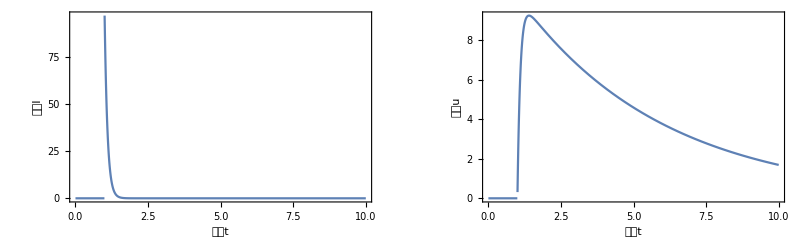

```mathematica
GraphicsGrid[{{figure1, figure2}}]
```

## 2、Time-dependent solution

```mathematica
Clear["Global`*"]
```

```mathematica
(*DSolve[τm*D[u[t],t]==-(u[t]-urest)+Is[t]*R,u[t],t];*)
(*u=urest+(R/τm)*Integrate[E^(-(t-s)/τm)*Is[s],{s,0,t}]*)
u=Integrate[E^(-(t-s))*Is[s],{s,0,t}]
a=D[u[t],t];
```

∫_0^t ⅇ^(s-t) Is[s]ⅆs

```mathematica
Clear["Global`*"]
a=DSolve[τx*D[x[t],t]==-x[t]+DiracDelta[t-tf],x[t],t];
x[t]=E^(-(t-tf)/τx)/τx*HeavisideTheta[t-tf];
b=DSolve[τs*D[Is[t],t]==-Is[t]+I0*x[t],Is[t],t];
Is[t]=1/(τs*τx)*E^(-t/τs)*I0*(-(E^(tf/τs)*τs*τx)/(-τs+τx)+(E^((t/τs)-(t/τx)+(tf/τx))*τs*τx)/(-τs+τx))*HeavisideTheta[t-tf]//Simplify

c=DSolve[τm*D[u[t],t]==-u[t]+R*Is[t],u[t],t];
u[t]=(E^(-(t/τm)-(t/τs)-(t/τx))*I0*R*(-E^((tf/τs)+(t/τm)+(t/τx))*τs*(τm-τx)+E^((tf/τm)+(t/τs)+(t/τx))*τm*(τs-τx)+E^((tf/τx)+(t/τm)+(t/τs))*τx*(τm-τs))*HeavisideTheta[t-tf])/((-τm+τs)*(τm-τx)*(τs-τx))//Simplify
```

((ⅇ^((-t+tf)/τs)-ⅇ^((-t+tf)/τx)) I0 HeavisideTheta[t-tf])/(τs-τx)

-((ⅇ^(-t (1/τm+1/τs+1/τx)) I0 R (-ⅇ^(tf/τs+t (1/τm+1/τx)) τs (τm-τx)+ⅇ^(tf/τm+t (1/τs+1/τx)) τm (τs-τx)+ⅇ^(t (1/τm+1/τs)+tf/τx) (τm-τs) τx) HeavisideTheta[t-tf])/((τm-τs) (τm-τx) (τs-τx)))